```mathematica
(*From muon to electron*)

A11= Cos[θ21]Cos[θ31]
A21= Sin[θ21] Cos[θ31]
A31= Sin[θ31] Exp[-I*σ]
A32= Sin[θ31]Exp[I*σ]
B11=-(Sin[θ21]Cos[θ32])-(Cos[θ21]Sin[θ32]Sin[θ31]Exp[I*σ])
B12= -(Sin[θ21]Cos[θ32])-(Cos[θ21]Sin[θ32]Sin[θ31]Exp[-I*σ])
B21=((Cos[θ21]Cos[θ32])-(Sin[θ21]Sin[θ32]Sin[θ31]Exp[I*σ]))
B22=((Cos[θ21]Cos[θ32])-(Sin[θ21]Sin[θ32]Sin[θ31]Exp[-I*σ]))
B31=Sin[θ32]Cos[θ31]
B32=B31
δm31=δm32+δm21
```

Cos[θ21] Cos[θ31]

Cos[θ31] Sin[θ21]

ⅇ^(-ⅈ σ) Sin[θ31]

ⅇ^(ⅈ σ) Sin[θ31]

-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]

-Cos[θ32] Sin[θ21]-ⅇ^(-ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]

Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32]

Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32]

Cos[θ31] Sin[θ32]

Cos[θ31] Sin[θ32]

δm21+δm32

```mathematica
P1=0
P2=4Re[((B22*A21*B11*A11)*(Sin[(((δm21)^2)*(l/e)*1.27)])^2)+((B32*A31*B21*A21)*(Sin[(((δm32)^2)*(l/e)1.27 )])^2)+((B32*A31*B11*A11)*(Sin[(((δm31)^2)*(l/e)*1.27)])^2)]
P3=2Im[(((B22*A21*B11*A11)Sin[(((((δm21)^2)*(l/e))/2))])+((B32*A31*B21*A21)Sin[((((δm32)^2)*(l/e))/2)])+((B32*A31*B11*A11)Sin[((((δm31)^2)*(l*e))/2)]))]
```

0

4 Re[ⅇ^(-ⅈ σ) Cos[θ21] Cos[θ31]^2 Sin[(1.27 l (δm21+δm32)^2)/e]^2 Sin[θ31] Sin[θ32] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32])+Cos[θ21] Cos[θ31]^2 Sin[(1.27 l δm21^2)/e]^2 Sin[θ21] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]) (Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])+ⅇ^(-ⅈ σ) Cos[θ31]^2 Sin[(1.27 l δm32^2)/e]^2 Sin[θ21] Sin[θ31] Sin[θ32] (Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])]

2 Im[ⅇ^(-ⅈ σ) Cos[θ21] Cos[θ31]^2 Sin[1/2 e l (δm21+δm32)^2] Sin[θ31] Sin[θ32] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32])+Cos[θ21] Cos[θ31]^2 Sin[(l δm21^2)/(2 e)] Sin[θ21] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]) (Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])+ⅇ^(-ⅈ σ) Cos[θ31]^2 Sin[(l δm32^2)/(2 e)] Sin[θ21] Sin[θ31] Sin[θ32] (Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])]

```mathematica
f[e_,σ_]=P1-P2+P3 /.{θ21->0.594371,
θ31->0.160875,
θ32->0.698357,
δm21->Sqrt[8*^-5],
δm32->-(Sqrt[2.3*^-3]),l->1300}
```

2 Im[0.452046 (0.634549-0.0576735 ⅇ^(-ⅈ σ)) (-0.428894-0.0853278 ⅇ^(ⅈ σ)) Sin[13/(250 e)]+0.0561937 ⅇ^(-ⅈ σ) (0.634549-0.0576735 ⅇ^(ⅈ σ)) Sin[1.495/e]+0.0831385 ⅇ^(-ⅈ σ) (-0.428894-0.0853278 ⅇ^(ⅈ σ)) Sin[0.989362 e]]-4 Re[0.452046 (0.634549-0.0576735 ⅇ^(-ⅈ σ)) (-0.428894-0.0853278 ⅇ^(ⅈ σ)) Sin[0.13208/e]^2+0.0831385 ⅇ^(-ⅈ σ) (-0.428894-0.0853278 ⅇ^(ⅈ σ)) Sin[2.51298/e]^2+0.0561937 ⅇ^(-ⅈ σ) (0.634549-0.0576735 ⅇ^(ⅈ σ)) Sin[3.7973/e]^2]

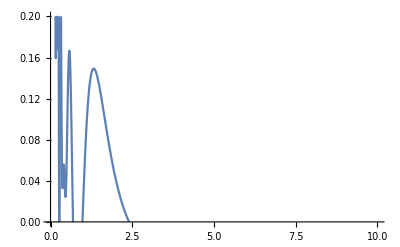

```mathematica
Plot[f[e,0],{e,0.1,10},PlotRange->{0,0.2}]
```

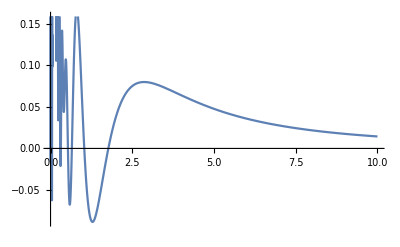

```mathematica
Plot[f[e,π],{e,0,10}]
```

```mathematica
Manipulate[Plot[f[e,σ],{e,0.1,10}],{σ,0,2π}]
```

```mathematica
Manipulate[Plot[f[e,-σ],{e,0.1,10}],{σ,0,2π}]
```

```mathematica
Manipulate[Plot[f[e,σ]-f[e,-σ],{e,0.1,10}],{σ,0,2π}]
```

```mathematica
Manipulate[Plot[f[e,σ]-f[e,-σ],{e,0.1,0.5}],{σ,0,2 π}]
```

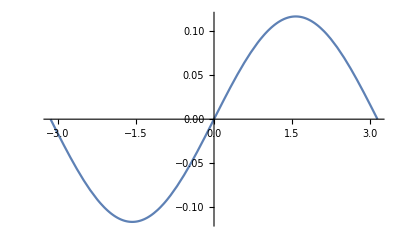

```mathematica
Plot[f[0.4,σ]-f[0.4,-σ],{σ,-π,π}]
```